```mathematica
f[x_] = (3x + π)/(√(1+ x^2 + √((1+x^2)^3)))
```

(π+3 x)/(√(1+x^2+√((1+x^2)^3)))

```mathematica
a = 0;
b = 6;
n1 = 6;
n2 = 10;
x0=2.4316;
graphic = Plot[f[x], {x, a, b},  PlotStyle ->{Purple, Thick}]
```

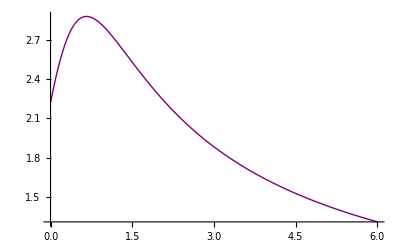

-Graphics-

```mathematica
Cheb1[i_]=Cos[(Pi (2 i+1))/(2 n1+2)];
```

```mathematica
Cheb2[i_]=Cos[(Pi (2 i+1))/(2 n2+2)];
```

```mathematica
data1=Table[{x1=(a+b)/2+(b-a)/2*Cheb1[i],f[x1]},{i,0,n1}]//N//Reverse;
```

```mathematica
data2=Table[{x2=(a+b)/2+(b-a)/2*Cheb2[i],f[x2]},{i,0,n2}]//N//Reverse;
```

```mathematica
{TableForm[data1],TableForm[data2]}
```

{0.0752163 | 2.37262
0.654506 | 2.88305
1.69835 | 2.42463
3. | 1.88196
4.30165 | 1.56122
5.34549 | 1.38984
5.92478 | 1.31489,0.0305357 | 2.28489
0.271104 | 2.67508
0.732751 | 2.87809
1.37808 | 2.59929
2.1548 | 2.20095
3. | 1.88196
3.8452 | 1.65653
4.62192 | 1.50261
5.26725 | 1.40091
5.7289 | 1.33895
5.96946 | 1.30958}

```mathematica
diftab1=Array[dif1,{n1+1,n1+1},{0,0}];
```

```mathematica
For[k=1,k≤n1,k++,For[i=n1,i≥n1-k,i--,dif1[i,k]=""]]
```

```mathematica
For[i=0,i≤n1,i++,dif1[i,0]=data1[[i+1,2]]]
```

```mathematica
For[k=1,k≤n1,k++,For[i=0,i≤n1-k,i++,dif1[i,k]=(dif1[i+1,k-1]-dif1[i,k-1])/(data1[[i+1+k,1]]-data1[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab1], {n1, n1 - 1}]
```

```mathematica
{{" 2.37262", " 0.88113", "-0.81342", " 0.28136", "-0.06294", " 0.01098", ""}, {" 2.88305", "-0.43916", " 0.00949", " 0.01536", "-0.00505", "", ""}, {" 2.42463", "-0.41691", " 0.06549", "-0.00835", "", "", ""}, {" 1.88196", "-0.24641", " 0.03506", "", "", "", ""}, {" 1.56122", "-0.16418", "", "", "", "", ""}, {" 1.38984", "", "", "", "", "", ""}, {" 1.31489", ", "", "", "", "", ""}}
```

```mathematica
diftab2=Array[dif2,{n2+1,n2+1},{0,0}];
```

```mathematica
For[k=1,k≤n2,k++,For[i=n2,i≥n2-k,i--,dif2[i,k]=""]]
```

```mathematica
For[i=0,i≤n2,i++,dif2[i,0]=data2[[i+1,2]]]
```

```mathematica
For[k=1,k≤n2,k++,For[i=0,i≤n2-k,i++,dif2[i,k]=(dif2[i+1,k-1]-dif2[i,k-1])/(data2[[i+1+k,1]]-data2[[i+1,1]])]]
```

```mathematica
PaddedForm[TableForm[diftab2], {n2, n2 - 1}]
```

```mathematica
{{" 2.284886061", " 1.621954326", "-1.683512124", " 0.664879227", "-0.130375309", " 0.003670660", " 0.006170230", "-0.002428102", " 0.000610911", "-0.000125538", " 0.000023238"}, {" 2.675076921", " 0.439765845", "-0.787559526", " 0.387927306", "-0.119475416", " 0.027208002", "-0.004978124", " 0.000771065", "-0.000104447", " 0.000012471", ""}, {" 2.878093619", "-0.432041706", "-0.056821513", " 0.061891323", "-0.022231469", " 0.005549090", "-0.001125769", " 0.000201017", "-0.000033382", "", ""}, {" 2.599285757", "-0.512844798", " 0.083501510", "-0.007302934", "-0.000650109", " 0.000444294", "-0.000121457", " 0.000026204", "", "", ""}, {" 2.200946493", "-0.377411824", " 0.065484296", "-0.009411786", " 0.001077826", "-0.000084145", "-1.143948703"×10^("-6"), "", "", "", ""}, {" 1.881958898", "-0.266717476", " 0.042264288", "-0.006057111", " 0.000777083", "-0.000088509", "", "", "", "", ""}, {" 1.656529909", "-0.198168078", " 0.028531312", "-0.003936531", " 0.000514259", "", "", "", "", "", ""}, {" 1.502607853", "-0.157595096", " 0.021116075", "-0.002844107", "", "", "", "", "", "", ""}, {" 1.400907597", "-0.134220159", " 0.017283522", "", "", "", "", "", "", "", ""}, {" 1.338945228", "-0.122083401", "", "", "", "", "", "", "", "", ""}, {" 1.309575827", "", "", "", "", "", "", "", "", "", ""}}
```

```mathematica
P1[x_]=1;P2[x_]=1;Pnr1[x_]=dif1[0,0];Pnr2[x_]=dif2[0,0];
```

```mathematica
For[i=0,i<n1,i++,P1[x_]=P1[x] (x-data1[[i+1,1]]);Pnr1[x_]=Pnr1[x]+dif1[0,i+1] P1[x]]
```

```mathematica
Pnr1[x]//Simplify
```

2.20542+2.43227 x-2.8814 x^2+1.33 x^3-0.311261 x^4+0.036391 x^5-0.0016854 x^6

```mathematica
For[i=0,i<n2,i++,P2[x_]=P2[x] (x-data2[[i+1,1]]);Pnr2[x_]=Pnr2[x]+dif2[0,i+1] P2[x]]
```

```mathematica
Pnr2[x]//Simplify
```

2.21897+2.21792 x-1.92048 x^2-0.564274 x^3+1.59653 x^4-1.05604 x^5+0.376426 x^6-0.0808287 x^7+0.0104631 x^8-0.000753672 x^9+0.000023238 x^10

```mathematica
graph1=ListPlot[data1,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graph2=ListPlot[data2,PlotStyle->{Darker,PointSize[0.02]}];
```

```mathematica
graph1Pnr=Plot[Pnr1[x],{x,a,b}];
```

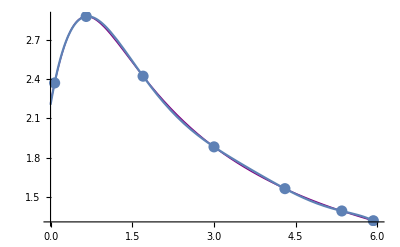

```mathematica
Show[graphic,graph1,graph1Pnr]
```

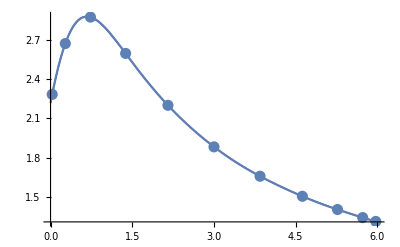

```mathematica
graph2Pnr=Plot[Pnr2[x],{x,a,b}];
Show[graphic,graph2,graph2Pnr]
```

```mathematica
Intf1=Interpolation[data1]
```

InterpolatingFunction[…]

```mathematica
Intf2=Interpolation[data2]
```

InterpolatingFunction[…]

```mathematica
graph1Intf=Plot[Intf1[x],{x,a,b}];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

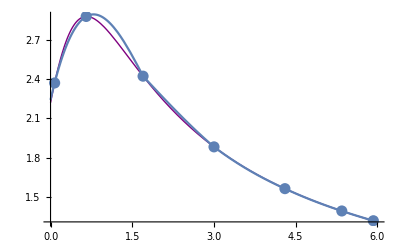

```mathematica
Show[graphic,graph1,graph1Intf]
```

```mathematica
graph2Intf=Plot[Intf2[x],{x,a,b}];
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

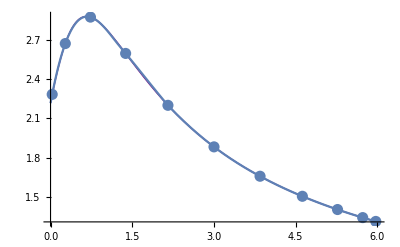

```mathematica
Show[graphic,graph2,graph2Intf]
```

```mathematica
Print["Pnr1[x0]=",Pnr1[x0],", Pnr2[x0]=",Pnr2[x0]]
```

Pnr1[x0]=2.06831, Pnr2[x0]=2.08511

```mathematica
Print["Intf1[x0]=",Intf1[x0],", Intf2[x0]=",Intf2[x0]]
```

Intf1[x0]=2.1036, Intf2[x0]=2.08455

```mathematica
Rnp1[x_]=Abs[f[x]-Pnr1[x]]//Simplify;
```

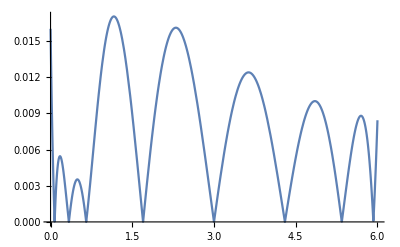

```mathematica
graphErrp1=Plot[Rnp1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrp1=FindMaximum[Rnp1[x],{x,a+0.2,b}]
```

{0.005451,{x→0.17328}}

```mathematica
RnI1[x_]=Abs[f[x]-Intf1[x]]//Simplify;
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

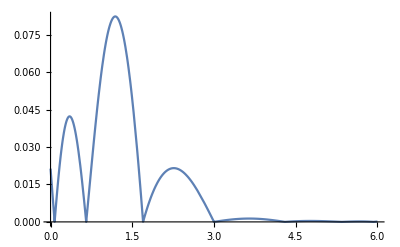

```mathematica
graphErrI1=Plot[RnI1[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI1=FindMaximum[RnI1[x],{x,a+0.2,b}]
```

{0.042269,{x→0.349463}}

```mathematica
Rnp2[x_]=Abs[f[x]-Pnr2[x]]//Simplify;
```

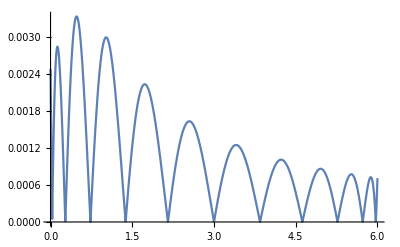

```mathematica
graphErrp2=Plot[Rnp2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrp2=FindMaximum[Rnp2[x],{x,2,4}]
```

{0.00222884,{x→1.72847}}

```mathematica
RnI2[x_]=Abs[f[x]-Intf2[x]]//Simplify;
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

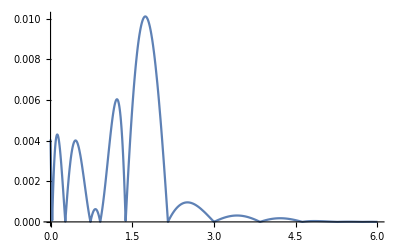

```mathematica
graphErrI2=Plot[RnI2[x],{x,a,b},PlotRange->Full]
```

```mathematica
maxErrI2=FindMaximum[RnI2[x],{x,0.5,2}]
```

{0.00400466,{x→0.45885}}